```mathematica
Manipulate[ParametricPlot[{Cos[α t]Sin[β t],Cos[α t]Cos[β t]},{t,0,tMax},PlotLabel->Style["Solución analítica", 15]],{α,0.1,4},{β,0.1,4},{tMax,1,40}]
```

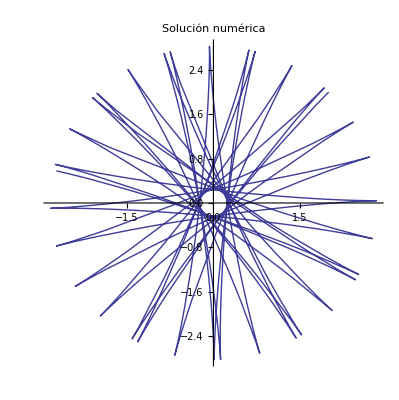

```mathematica
ω = 1;
Ω = 0.1;
ϕ=1;
s=NDSolve[{x''[t]==-ω^2*x[t]-2 Ω*Sin[ϕ]*y'[t],y''[t]==-ω^2*y[t]+2 Ω*Sin[ϕ]*x'[t],x[0] ==2,y[0] == 2,x'[0] ==0,y'[0]==0},{x,y},{t,100}];
ParametricPlot[Evaluate[{x[t],y[t]}/.s],{t,0,100},PlotLabel->Style["Solución numérica", 15]]
```